## Initialization

```mathematica
$path="D:\\Documents\\aDependence\\";
```

```mathematica
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_energyVs2.mx"];
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_efV1.mx"];
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_efVs2.mx"];
```

```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<1,Fa,0];
V4[r_,Ff_,Fg_]=-α/r+Ff E^(-Fg r);
V5[r_,Fi_,Fj_]=-α/r+Fi E^(-Fj r^2);
```

```mathematica
Fa=-2.71562984954227987707220753658717987150651086990482099679916347484158640580824`50.;
```

```mathematica
{Ff,Fg}={-4.20415644616125582469299138439140113373493210258692526366760104908016252690683`50.,1.88979567639491639010430213789778028047296373449456361136288297937037496900499`50.};
```

```mathematica
{Fi,Fj}={Fi,Fj}/.{Fi->-2.647828543053613773374298558957824633572173998851964865568`30.,Fj->1.0017713271893313754426035031926440089474493688810307925058`30.};
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[evShifted],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
(*time1=SessionTime[];*)
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
(*time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},{opt___},{opt2nd___}]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1},opt2nd]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)]]
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]]
```

```mathematica
enV1=EigenEnergy[V1[r,Fa],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
Export[$path<>"enV1.dat",enV1,"CSV"];
```

```mathematica
enV1=Flatten@Import[$path<>"enV1.dat","CSV"];
```

```mathematica
AbsoluteTiming[efV1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[PrintTemporary[n];
efunction[[n]]=First@Eigenfunsin[V1[r,Fa],enV1[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.01},{Exclusions->1}];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

```mathematica
lapV1=Table[lap[efV1[[n]]/(√(4π)r),r],{n,20}];
```

Calculation

### Determine c_1a

```mathematica
δexpminus10=δ50e[10^-10,V1[r,Fa]];
δexpminus9=δ50e[10^-9,V1[r,Fa]];
δexpminus5=δ50e[10^-5,V1[r,Fa]];
δ50V=δ50[V1[r,Fa]];
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031976961469011990340175947388312022842768758134) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001587464132865018998597875314097697935557) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095049698306647997185436012980973711952116617) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898684) is less than WorkingPrecision (50.).

{0.001,-0.73208746431028526245311528777683686832243445809232}    0.640632

NDSolve::precw: The precision of the differential equation ({{2 (0.003+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031971676417742421692484655632768966490285659951) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001587464132865018998597875314097697935557) is less than WorkingPrecision (50.).

{1/1000000,-0.031960789405125522933373507687582716449828744781774}    0.7187568

{1/1000000000,-0.0010111998140872207752808208261703652631523828719599}    0.796884

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22631) is less than WorkingPrecision (50.).

{0.01,-0.88670402762674631122717109111765016717471389247589}    0.8906361

NDSolve::precw: The precision of the differential equation ({{2 (0.03+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==35870.5) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095049698306647997185436012980973711952116617) is less than WorkingPrecision (50.).

{0.003,1.57076844873560063803161059293930907694661482058}    0.45313

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031976909224997864261154138264165866246216981177) is less than WorkingPrecision (50.).

{1/100000,-0.10060964977929146302920898313696792694331731557305}    0.359379

NDSolve::precw: The precision of the differential equation ({{2 (0.007+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000000,-0.0031976800235278821815007097532292797715298185928745}    0.359378

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.20582) is less than WorkingPrecision (50.).

{0.03,-0.20298505215399587250713295435250322849670206154992}    0.515629

NDSolve::precw: The precision of the differential equation ({{2 (0.07+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0166057) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010111836353197228798292517594804279873741813862) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.3137410221526808473123574012541655877376698201) is less than WorkingPrecision (50.).

{0.007,0.016604178728464292214601585968525799790046011557589}    0.406255

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1/10000000,-0.010111491731830732719170441925669522776415359340761}    0.421879

{1/10000,-0.30401507950111997826713021892165681010205303319686}    0.437504

NDSolve::precw: The precision of the differential equation ({{2 (0.3+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.811462) is less than WorkingPrecision (50.).

{0.07,0.68169074216635950683681615527649603106534146201229}    0.500006

NDSolve::precw: The precision of the differential equation ({{2 (0.1+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.614463) is less than WorkingPrecision (50.).

{0.3,0.55098654513026699261247024430075427761020475265127}    0.687512

NDSolve::precw: The precision of the differential equation ({{2 (0.7+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.147226) is less than WorkingPrecision (50.).

{0.1,-0.14617618177335730464091724674502957670008967138439}    0.70313

FindRoot::precw: The precision of the argument function (Tan[δ]==10.04983271206702846207961618022003619570185374) is less than WorkingPrecision (50.).

{1,1.47161864503671708577806852705949807570607304415}    1.10939

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.82382) is less than WorkingPrecision (50.).

{0.7,-1.069259789592027712878623874602989877147311062589}    0.8750057

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.03219894563313406668363475666893071855716533175) is less than WorkingPrecision (50.).

{3,-0.032187824893958698621560949873406331585183920121249}    1.468762

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.96249605362685539392366192572858232057638771238) is less than WorkingPrecision (50.).

{7,-0.7662901597075154258059144113406261328686158728487}    2.687527

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.848336981536975011352598864634846824296146574) is less than WorkingPrecision (50.).

{10,-1.0748683557181722316154300446515310649841369657651}    2.812532

```mathematica
nRange=20;
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{start_,end___},opt___]:=Module[{findroot},
Print[a];
findroot=FindRoot[hhhc1[10^-10,a,c1]==δexpminus10,{c1,start,end},opt];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a={};
```

```mathematica
Module[{table},
table=ParallelTable[Block[{c1,a},
a=10^loga;
c1=Determinec1[a,{0},{MaxIterations->If[a>10,200,100],PrecisionGoal->10,WorkingPrecision->50}];
{a,c1}],{loga,DeleteDuplicates[Join[Range[2,1,-0.02],Range[1,0,-0.02],Range[0,-1,-0.1],Range[-1,-3,-0.4]]]}];
c1a=DeleteDuplicates@Sort[c1a~Join~table]
]
```

100.

63.0957

39.8107

25.1189

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.001697979230839371255597111761846442876101896285) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825568615731125747527397203589864186214156) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870131827447159790285729474411013289881625) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.001697979230839371255597111761846442876101896285) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-1.49951×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156082226654886369679990199569147367450379916) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825568615731125747527397203589864186214156) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870131827447159790285729474411013289881625) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-9.46129×10^-12 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0016979789639632308645647528601905605311581397931) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-2.37657×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825572758629025120772111693799303613160617) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870525243164726960710465842933993016136078) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156082226654886369679990199569147367450379916) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-3.76661×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156083757748849528015936859001896362469132464) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-6.120741468506836468046560399441002788684107471797

95.4993

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

0.69179687713138952834674838491382552537514938119384

60.256

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.9379631270453782680326219795932424401485594245277

38.0189

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-5.3006852416886884839638878512306900158261601697944

91.2011

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-22.40270845719532345254882361825183060573671837337

23.9883

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-4.5162642712061551879657182939282334662994109850555

87.0964

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.268283556561031752434870595164212698471521665275

36.3078

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-137.02013969963230331490215944856326409685929468159

57.544

-3.7656013985448125670396127359240156380491502913463

83.1764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-8.0620544646229743045546599918742079687956870459

22.9087

-3.0468718857514207390104841642562323743303590625331

79.4328

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-10.341662556144778260497567493865932286294250705189

54.9541

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-2.6197834524352149513077852022104554025917766413308

34.6737

-2.3582981209363875029767583354517619925044824569236

75.8578

-1.6981444141075211225791196740924160121328488289126

72.4436

-1.9901193077687418632231456891856140706435827729396

33.1131

-25.032127658393723135272040567591442607673276883426

52.4807

-1.0647119064610705990340480500719538836853119009249

69.1831

-1.3769619542640447926333153718480289919566346618958

31.6228

-8.532949972897958549125023541142092674414432320682

50.1187

-0.4563336280993621970777712875338706128655759906857

66.0693

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-79.623576453147421568852857162030998134252361247854

21.8776

0.12863024634617541808092981853686306159276074742087

15.8489

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000652910489955880113546166917628975402602190245665) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000652910489955880113546166917628975402602190245665) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-5.96967×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00065291049039470811409662598153906458706963875939) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-0.77800703247733869754420269400164570818899754352606

30.1995

-22.299717932610193646964748854252961153569404916663

47.863

-6.8649317935249550144548831225509284071567095517771

20.893

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-2.9132772236998084428923954763239466974587758531705

15.1356

-0.19099041566484302758773081743393899651487214521178

28.8403

-6.8755931546099602598185064793680811319522799610925

45.7088

0.38629074338119372136373361534769706747826127705641

27.5423

-6.285490267734235848192256624334108281176914555719

19.9526

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-2.3508490097354410971154328394685198843481736604692

14.4544

-6.0976221017454129798428682827371049320548174932289

43.6516

-5.3502725561094151523173243611027971940980051808285

41.6869

-5.7149647404919055030463720083104708497553722663313

19.0546

-40.598841317968419308884777985728767531418007549242

26.3027

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-1.7852311176105152232921443021610368012342808362228

13.8038

-4.6311737809377209302783742155702003282202304763362

10.

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575489469291939497592549879868890656703718613) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575489469291939497592549879868890656703718613) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-9.46129×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575490619253753998743047466437804865337191654) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-5.1507177013207277839398290559433657578401760880939

18.197

-1.2160195664180096264762623929979836598211365091709

13.1826

-23.108079248863538147697603559794729047732647966103

6.30957

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381524771803805621294508526919277259435239) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381524771803805621294508526919277259435239) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-1.49951×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381526560559240814728520309971721314179699) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-4.5903587065389087206591182012320964746375205893677

17.378

-0.64308257554846425284222084809452345363051215150439

12.5893

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-36.076873658543385391287121548593050781450038655635

9.54993

-4.0317886408959938783986946388655030520684301397992

16.5959

-0.066509779561596966376400259382618083171418673352411

12.0226

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-9.2094441978311888159556433527698188863659887065037

6.0256

-3.4732354477899047798679254707468233544259115849859

3.98107

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146167682903229914061418522311799381625457) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146167682903229914061418522311799381625457) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-2.37657×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146508317488428220163767037076939316116899) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

0.51343827474911459706512076686814375097114831060102

11.4815

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-13.243226266999335801642187526448644305118685846059

9.12011

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-36.75867155239539154698880405237839589639242215924

5.7544

-14.856809473283464911036908072925701234119597285059

10.9648

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-12.822984472019898343251972328326042320620721202105

8.70964

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-4.0785142322940842923245929275520728950829164641257

3.80189

-14.462982434824535618825483873649540056211470432509

10.4713

-12.395464422439176169512125369155401197275757777321

8.31764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-8.2400835061104775097930189758226635822790673177579

5.49541

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.5332571920555867722250318754834670892119822139401

3.63078

-11.960574130521421188194361195848791910236688879476

7.94328

-63.322071024830596824238447807460088801863271697465

2.51189

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577889898683544697998544264129055361964091685) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577889898683544697998544264129055361964091685) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-3.76661×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577887967918849532975581523052115611852350512) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-7.744167103304586078353871322048517197860763408869

5.24807

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-2.9830871176263418404501146583819949539908311563602

3.46737

-11.518435681890636307320461032979250934319957031937

7.58578

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

1.5916709821450201147411605088533670965419107579114

2.39883

-7.2404449048261001651219892357884389443793280936594

5.01187

-2.4276897491675012957019341019183585636877513360554

3.31131

-11.069356981561868740613277261182397597346011366979

7.24436

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-191.12380708974588860644378206946105962161363521427

2.29087

-10.61372151507658569681045605623586402910767242588

6.91831

-1.8668194887699347312727589123906343577379980862336

3.16228

-6.7290759633617682472882259692948537140722150770563

4.7863

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-39.192695117763156176556585236103524773205251110989

2.18776

-10.151836581363769348032330566127409551812605135198

6.60693

-1.3004696719228856375602636738686082069012169828638

3.01995

-6.2105459902724732868202345029972100257898109769449

4.57088

-9.6838006535698891948311641444676817183423228260796

1.65959

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588257256615862746155046428433718260457783) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588257256615862746155046428433718260457783) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-5.70099×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588665527541510154229912604182576454104279) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-0.72898404596109142993844932238431853734265575988625

2.88403

-108.34746895041058557338217338270511825514617254658

2.0893

-5.6855581458116286282473581854496611153889013287573

4.36516

-0.15306897571695463845310386914351099418851042762922

2.75423

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-233.47471172805161797237166274964723102660463759089

1.58489

-39.281918389871367261874589902110095035827654064144

1.99526

-5.1548597613072661736260355130701524129500676698661

4.16869

0.4263122231680240613521597640254829708133673578155

2.63027

-39.275258938906855585704405620755236194574034139247

1.90546

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-238.73993002991917967641602972995349000776570987228

1.51356

-4.6190626551272205991631492542376153427115964295744

1.09648

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089367901094246503744926379405179725908289082) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089367901094246503744926379405179725908289082) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-8.6288×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089368022156930929276732532001698633813955792) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

1.0081511189305356213187938008491882082131684522852

0.199526

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971241520645525842660423816735852021610647) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971241520645525842660423816735852021610647) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-4.74188×10^-9 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971259847355107659603072979101828654726458) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-244.24336866445309004184564032033793741071486804734

1.44544

-217.96542103647017880600541726320267192725730728968

1.8197

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-297.11593013097171239313675430144301041268223166013

1.04713

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-48.361169402701886482193042478951546172388727033416

0.158489

-126.30413571689851537867777237772795087252901079108

1.38038

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-54.96124226064771812490580721604621208642148605057

0.125893

-223.17501218409677220088707607313984594463960329022

1.7378

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-307.17215567509266273963052628448005407498324660637

1.

-128.90263746099006942770199815056907635825210741056

1.31826

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-64.828940604733754217113259457349032779206173929262

0.1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-317.86579627978595042823547642910422322583267279523

0.794328

-228.32170118582455513928246200515013788145445764447

-78.720890480477566940850554047487551671132179274005

0.0398107

-131.77317784922018294302868451910073620964025664651

1.25893

-181.34101153387684814364853698415345329745758590435

0.630957

-201.8467537424278558219570205118794932023320894833

0.0158489

-134.92961885857829794105887968317987587635149661528

1.20226

-48.209320250507085560500166467269704332940347298029

0.501187

-560.82597366576343511359599446385364873921539931297

0.00630957

-138.37738035595069771900120498708843057753220366632

1.14815

-47.101699628254689119310954509009652673699153585368

0.398107

-287.70407298798715855414800423360103748797036011145

-44.57719359266257172891536351168699289370007943224

0.316228

-43.365748540097154076342365847639581979053031816896

0.251189

-44.565270483796866237316425468454637766064618115124

-2.9802777135181724235679645573782181600108717556217×10^-7

0.00251189

-2.9802777135181724235679645573782181600108717557382×10^-7

0.001

-2.9802777135181718941723725210330938118252640146607×10^-7

{{0.001,-2.9802777135181718941723725210330938118252640146607×10^-7},{0.00251189,-2.9802777135181724235679645573782181600108717557382×10^-7},{0.00630957,-2.9802777135181724235679645573782181600108717556217×10^-7},{0.0158489,-560.82597366576343511359599446385364873921539931297},{0.0398107,-201.8467537424278558219570205118794932023320894833},{0.1,-78.720890480477566940850554047487551671132179274005},{0.125893,-64.828940604733754217113259457349032779206173929262},{0.158489,-54.96124226064771812490580721604621208642148605057},{0.199526,-48.361169402701886482193042478951546172388727033416},{0.251189,-44.565270483796866237316425468454637766064618115124},{0.316228,-43.365748540097154076342365847639581979053031816896},{0.398107,-44.57719359266257172891536351168699289370007943224},{0.501187,-47.101699628254689119310954509009652673699153585368},{0.630957,-48.209320250507085560500166467269704332940347298029},{0.794328,-181.34101153387684814364853698415345329745758590435},{1.,-317.86579627978595042823547642910422322583267279523},{1.04713,-307.17215567509266273963052628448005407498324660637},{1.09648,-297.11593013097171239313675430144301041268223166013},{1.14815,-287.70407298798715855414800423360103748797036011145},{1.20226,-138.37738035595069771900120498708843057753220366632},{1.25893,-134.92961885857829794105887968317987587635149661528},{1.31826,-131.77317784922018294302868451910073620964025664651},{1.38038,-128.90263746099006942770199815056907635825210741056},{1.44544,-126.30413571689851537867777237772795087252901079108},{1.51356,-244.24336866445309004184564032033793741071486804734},{1.58489,-238.73993002991917967641602972995349000776570987228},{1.65959,-233.47471172805161797237166274964723102660463759089},{1.7378,-228.32170118582455513928246200515013788145445764447},{1.8197,-223.17501218409677220088707607313984594463960329022},{1.90546,-217.96542103647017880600541726320267192725730728968},{1.99526,-39.275258938906855585704405620755236194574034139247},{2.0893,-39.281918389871367261874589902110095035827654064144},{2.18776,-108.34746895041058557338217338270511825514617254658},{2.29087,-39.192695117763156176556585236103524773205251110989},{2.39883,-191.12380708974588860644378206946105962161363521427},{2.51189,1.5916709821450201147411605088533670965419107579114},{2.63027,1.0081511189305356213187938008491882082131684522852},{2.75423,0.4263122231680240613521597640254829708133673578155},{2.88403,-0.15306897571695463845310386914351099418851042762922},{3.01995,-0.72898404596109142993844932238431853734265575988625},{3.16228,-1.3004696719228856375602636738686082069012169828638},{3.31131,-1.8668194887699347312727589123906343577379980862336},{3.46737,-2.4276897491675012957019341019183585636877513360554},{3.63078,-2.9830871176263418404501146583819949539908311563602},{3.80189,-3.5332571920555867722250318754834670892119822139401},{3.98107,-4.0785142322940842923245929275520728950829164641257},{4.16869,-4.6190626551272205991631492542376153427115964295744},{4.36516,-5.1548597613072661736260355130701524129500676698661},{4.57088,-5.6855581458116286282473581854496611153889013287573},{4.7863,-6.2105459902724732868202345029972100257898109769449},{5.01187,-6.7290759633617682472882259692948537140722150770563},{5.24807,-7.2404449048261001651219892357884389443793280936594},{5.49541,-7.744167103304586078353871322048517197860763408869},{5.7544,-8.2400835061104775097930189758226635822790673177579},{6.0256,-36.75867155239539154698880405237839589639242215924},{6.30957,-9.2094441978311888159556433527698188863659887065037},{6.60693,-9.6838006535698891948311641444676817183423228260796},{6.91831,-10.151836581363769348032330566127409551812605135198},{7.24436,-10.61372151507658569681045605623586402910767242588},{7.58578,-11.069356981561868740613277261182397597346011366979},{7.94328,-11.518435681890636307320461032979250934319957031937},{8.31764,-11.960574130521421188194361195848791910236688879476},{8.70964,-12.395464422439176169512125369155401197275757777321},{9.12011,-12.822984472019898343251972328326042320620721202105},{9.54993,-13.243226266999335801642187526448644305118685846059},{10.,-36.076873658543385391287121548593050781450038655635},{10.4713,-63.322071024830596824238447807460088801863271697465},{10.9648,-14.462982434824535618825483873649540056211470432509},{11.4815,-14.856809473283464911036908072925701234119597285059},{12.0226,0.51343827474911459706512076686814375097114831060102},{12.5893,-0.066509779561596966376400259382618083171418673352411},{13.1826,-0.64308257554846425284222084809452345363051215150439},{13.8038,-1.2160195664180096264762623929979836598211365091709},{14.4544,-1.7852311176105152232921443021610368012342808362228},{15.1356,-2.3508490097354410971154328394685198843481736604692},{15.8489,-2.9132772236998084428923954763239466974587758531705},{16.5959,-3.4732354477899047798679254707468233544259115849859},{17.378,-4.0317886408959938783986946388655030520684301397992},{18.197,-4.5903587065389087206591182012320964746375205893677},{19.0546,-5.1507177013207277839398290559433657578401760880939},{19.9526,-5.7149647404919055030463720083104708497553722663313},{20.893,-6.285490267734235848192256624334108281176914555719},{21.8776,-6.8649317935249550144548831225509284071567095517771},{22.9087,-79.623576453147421568852857162030998134252361247854},{23.9883,-8.0620544646229743045546599918742079687956870459},{25.1189,-22.40270845719532345254882361825183060573671837337},{26.3027,-23.108079248863538147697603559794729047732647966103},{27.5423,-40.598841317968419308884777985728767531418007549242},{28.8403,0.38629074338119372136373361534769706747826127705641},{30.1995,-0.19099041566484302758773081743393899651487214521178},{31.6228,-0.77800703247733869754420269400164570818899754352606},{33.1131,-1.3769619542640447926333153718480289919566346618958},{34.6737,-1.9901193077687418632231456891856140706435827729396},{36.3078,-2.6197834524352149513077852022104554025917766413308},{38.0189,-3.268283556561031752434870595164212698471521665275},{39.8107,-3.9379631270453782680326219795932424401485594245277},{41.6869,-4.6311737809377209302783742155702003282202304763362},{43.6516,-5.3502725561094151523173243611027971940980051808285},{45.7088,-6.0976221017454129798428682827371049320548174932289},{47.863,-6.8755931546099602598185064793680811319522799610925},{50.1187,-22.299717932610193646964748854252961153569404916663},{52.4807,-8.532949972897958549125023541142092674414432320682},{54.9541,-25.032127658393723135272040567591442607673276883426},{57.544,-10.341662556144778260497567493865932286294250705189},{60.256,-137.02013969963230331490215944856326409685929468159},{63.0957,0.69179687713138952834674838491382552537514938119384},{66.0693,0.12863024634617541808092981853686306159276074742087},{69.1831,-0.4563336280993621970777712875338706128655759906857},{72.4436,-1.0647119064610705990340480500719538836853119009249},{75.8578,-1.6981444141075211225791196740924160121328488289126},{79.4328,-2.3582981209363875029767583354517619925044824569236},{83.1764,-3.0468718857514207390104841642562323743303590625331},{87.0964,-3.7656013985448125670396127359240156380491502913463},{91.2011,-4.5162642712061551879657182939282334662994109850555},{95.4993,-5.3006852416886884839638878512306900158261601697944},{100.,-6.120741468506836468046560399441002788684107471797}}

```mathematica
Export[$path<>"c1aV1.dat",c1a,"CSV"];
```

```mathematica
c1a=Import["D:\\Documents\\aDependence\\c1aV1.dat","CSV"];
```

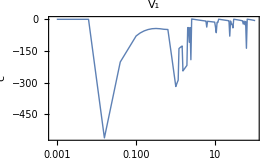

```mathematica
ListLogLinearPlot[c1a,ImageSize->270,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["V_1",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
(*Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\V1_c1_veus_a.eps",%];*)
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=1;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
Clear[c2,d1]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-36.2960467438514938819265262051,5.83238717691578772000732634051,0.000048419896,0.00015311719}

{-36.4745234751600742417665109283,5.31874642496672795610907338678,4.4920646×10^-6,0.00001420516}

{-36.9843693385032225023324358357,4.89142126362096524155599734732,3.509951×10^-6,0.000011099443}

{-36.9446028390687265349163285747,4.89182286431052761548226752832,3.1131044×10^-8,9.8445481×10^-8}

{-37.1800711874715597862402885555,4.69970695013297972467892467177,-2.593815×10^-8,-8.2023248×10^-8}

{-37.1869576573549728246442839686,4.69411914182335661765633556905,-2.5902834×10^-8,-8.1911572×10^-8}

{-37.1939142379074901152003462084,4.68847529004580597665505941648,-2.5868556×10^-8,-8.1803174×10^-8}

{-37.2007793396540431745328232243,4.68290651489019381527430673703,-2.5833155×10^-8,-8.1691229×10^-8}

{-37.2076810254911364504933332345,4.67730890303732209340705729218,-2.5798341×10^-8,-8.158114×10^-8}

{-37.2123935219386110390323171683,4.67348727558430569249019177476,-2.5779435×10^-8,-8.1521353×10^-8}

{-37.2116958994458717956512139856,4.67429117410172459642392321806,6.1583733×10^-13,2.3480253×10^-12}

{-37.2117467651313705412034906459,4.67424991790377539922785500836,-4.299018×10^-15,3.8697217×10^-13}

{-37.2121505125253527801144873917,4.67392249166173220214785437282,-1.6143622×10^-13,-1.1001297×10^-13}

{-37.2121430104622537728499902907,4.67392857583323010404114302465,-1.2989479×10^-13,-1.0268812×10^-14}

{-37.2121014362598278920470775094,4.67396229092024646394797470813,-1.2831535×10^-13,-5.2666223×10^-15}

{-37.2121014648333776771116544368,4.67396226774819063352402207675,-1.2831535×10^-13,-5.2666256×10^-15}

{-37.212099223101870382281335503,4.67396408570673510769114964292,-1.2831513×10^-13,-5.2655061×10^-15}

{-37.212100216338237988712508461,4.67396328034960778671055775111,-1.153674×10^-13,3.5678616×10^-14}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-37.2121002163382379887125084611,4.673963280349607786710557751}

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

{-1.56857,-0.181026,-0.0702548,-0.0371286,-0.022921,-0.0155471,-0.0112345,-0.00849604,-0.00664931,-0.00534528,-0.00439039,-0.00367028,-0.00311383,-0.00267497,-0.00232275,-0.00203578,-0.00179888,-0.00160105,-0.00143415,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$18445]-u''[r$18445]/2==e$18444 u[r$18445],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-1.56857486316823526449817119727,-0.181026486502200123675705180226,-0.0702548306748202866850762648015,-0.0371286504340278333757046949662,-0.0229209806930553923449713172592,-0.0155471285731900089246725395037,-0.0112344870402446863170924290933,-0.00849604147684494918335511584413,-0.00664930878714141407252073345406,-0.00534528135305988604487347380903,-0.00439039502315246896598119464161,-0.00367027996033755567807484672212,-0.00311383431045679262123273760449,-0.00267496954903121891315458344947,-0.00232274818836380797322803053136,-0.00203577720433811139456621377974,-0.00179888076727626840009449838825,-0.00160105161240657239509440304341,-0.00143414881331963075702649154775,-0.00129204659152907178136928323908}

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V1.dat",energyVs2,"CSV"];
```

```mathematica
Flatten@Import["D:\\Documents\\aDependence\\a=1c2d1V1.dat"];
```

```mathematica
Abs@((energyVs2-enV1)/enV1)
```

{0.2927657392381087851773548494,0.0064463511133993828717500285,0.0012514656093242190077759126,0.00044972607668059290346393573,0.000211958018985113354710635,0.0001166527606372310853595756,0.0000710332673609493699833599,0.00004645725013354049857478128,0.00003204599745162798346051518,0.0000230367981800433871668704,0.0000171153342989375254126919,0.0000130631669864717629916509,0.0000101966179551034744157583,8.11161654300912667905132×10^-6,6.5588014962841960816032×10^-6,5.3785589775546737422041×10^-6,4.4654705493560757863605×10^-6,3.7479944193142057804097×10^-6,3.1764102352105329030403×10^-6,2.7154294765810146326918×10^-6}

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.5685748631682357783135750207 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371286504340277450018934854778 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112344870402446657082844890104 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534528135305987770883163026748 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439039502315246600456786479796 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229209806930553394506359970815 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849604147684492760940495784873 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.181026486502200639496571132582 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367027996033754989959631052105 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155471285731899931056933177378 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664930878714140590975166624439 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.070254830674820536213199127543 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0031138343104567922694241488144 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232274818836380907089365305896 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179888076727626922778443801348 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143414881331963196920371232907 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267496954903121954591652151628 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203577720433811209940786580856 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160105161240657339489155051192 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129204659152907310452860120281 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

NIntegrate::precw: The precision of the argument function (5.51037167116×10^-1492 ⅇ^(-r^2/2) r InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-4.74931874869×10^-471 ⅇ^(-r^2/2) r InterpolatingFunction[«1»][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (2.35528×10^-271 ⅇ^(-r^2/2) r «1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.0117980183079960839798961717611,-0.000312967977784210299407809740493,-0.000190087562929555318484932285327,-0.000123446553426064265225113047046,-0.0000875621143653779750786898910937,-0.0000660458824647893419111016711737,-0.000052035138421078128325020997704,-0.0000423370980912647378794289309212,-0.0000353058034312754028362604687306,-0.0000300201420053736842683586781594,-0.0000259299832089318409196471514801,-0.0000226891033900065991852979025862,-0.0000200700619627677047193319086626,-0.0000179180199397507266123999432172,-0.0000161243382917728893476348896973,-0.0000146108017585063145357199494855,-0.0000133198287015424434402564949911,-0.0000122081940350169826454080128407,-0.0000112428883377383712893319189951,-0.0000103983168585812274869981101461}

NIntegrate::precw: The precision of the argument function (8.67862044768×10^-1491 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-7.47999177997×10^-470 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (3.70948×10^-270 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-0.0192936355834942867119156102405,-0.00720083637765447713429944001429,-0.00325264385169331822691350897826,-0.00196266764871568209854721484836,-0.00135107885276725784730443256009,-0.00100371248563163406380890690765,-0.000783871111308987054572237391148,-0.000634253684587910530351442878081,-0.000526954020094746249515696257509,-0.000446891674296342535223616195803,-0.0003852662162622432989804448864,-0.000336628190408688143452040211222,-0.000297439805710531392787534863805,-0.000265313895854775763073587569531,-0.00023858702430938670058530922996,-0.000216068060036572323535387506082,-0.000196883905471531189841828357687,-0.000180381469615937729196725894187,-0.000166063471201693861160667627222,-0.00015354527412130108618133578491}

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV1[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000161243382917728893476348896973 γ-0.00023858702430938670058530922996 η)==0.00744264,4 π (-0.0000103983168585812274869981101461 γ-0.00015354527412130108618133578491 η)==0.004795}) is less than WorkingPrecision (30.).

{{0,-19.4269837778888170038400521705},{0,-1.16946654608803389992392423397}}

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000161243382917728893476348896973 γ-0.00023858702430938670058530922996 η)==0.00744264,4 π (-0.0000103983168585812274869981101461 γ-0.00015354527412130108618133578491 η)==0.004795}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-0.0000161243382917728893476348896973 γ-0.00023858702430938670058530922996 η)==0.0074352,4 π (-0.0000103983168585812274869981101461 γ-0.00015354527412130108618133578491 η)==0.0047902}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-0.0000161243382917728893476348896973 γ-0.00023858702430938670058530922996 η)==0.00742774,4 π (-0.0000103983168585812274869981101461 γ-0.00015354527412130108618133578491 η)==0.0047854}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V1.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V1.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

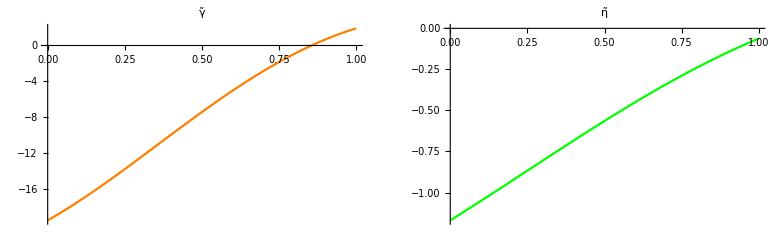

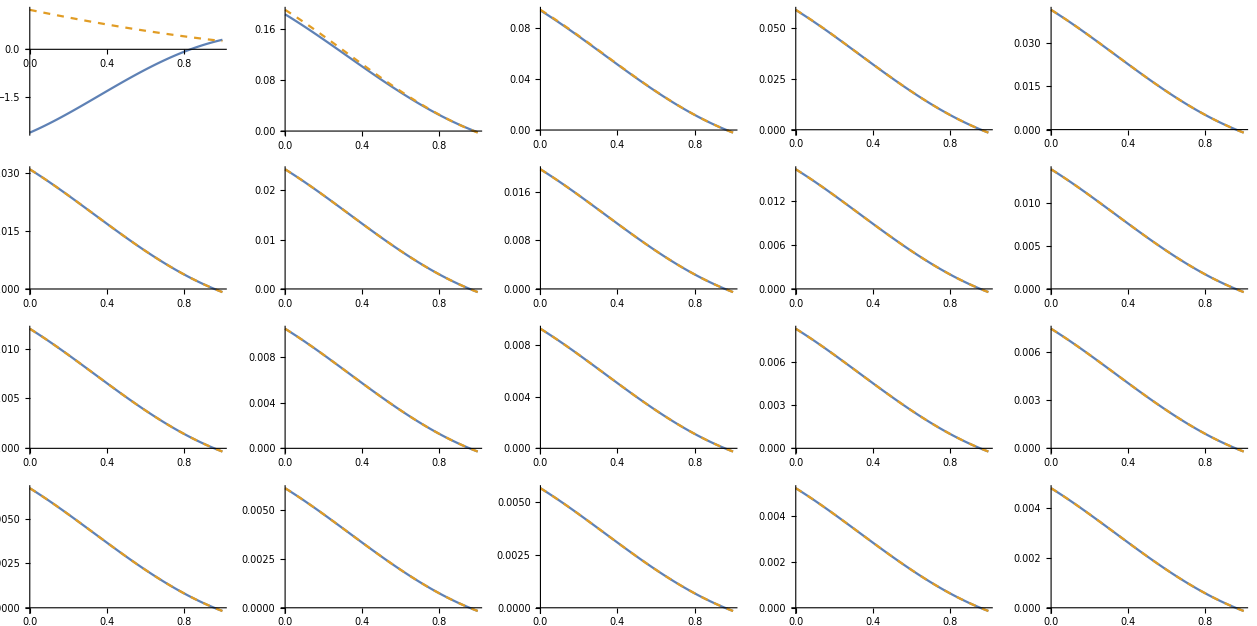

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV1[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV1[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000161243382917728893476348896973 γ-0.00023858702430938670058530922996 η)==-0.169342,4 π (-0.0000103983168585812274869981101461 γ-0.00015354527412130108618133578491 η)==-0.109109}) is less than WorkingPrecision (30.).

{{0.1,473.572068485836885573110440572},{0.1,24.4763442827400017772842547478}}

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V1.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V1.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

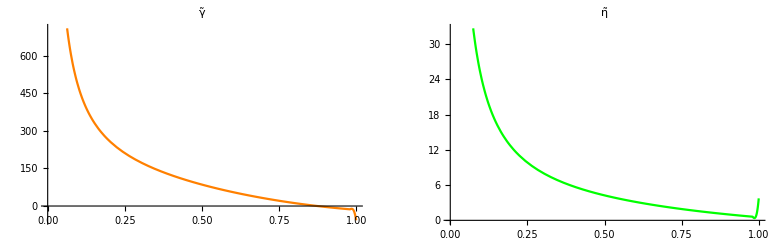

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

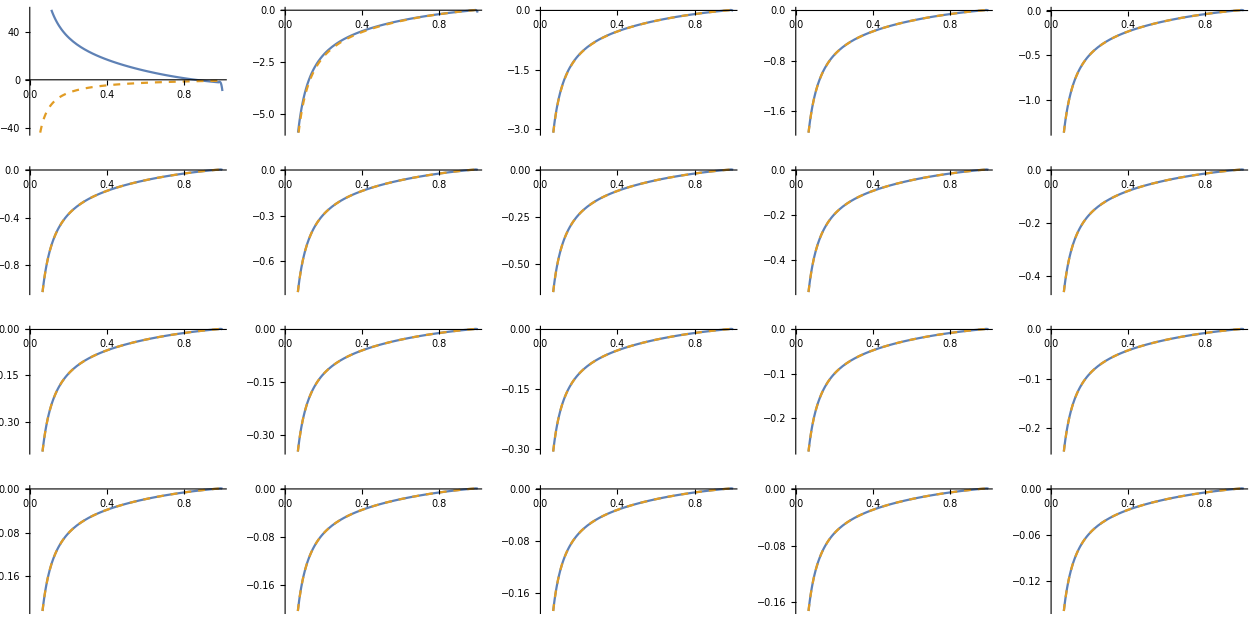

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV1[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.7;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-1},{d1,1}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
Clear[c2,d1]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031976961480548731973385648748592179213571962958) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001587107346343220892957555530244803859291) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031976961480548731973385648748592179213571962958) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-0.999999999999999999999999999949,0.999999999999999999999999999984}

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

$Aborted

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V1.dat",energyVs2,"CSV"];
```

```mathematica
Flatten@Import["D:\\Documents\\aDependence\\a=1c2d1V1.dat"];
```

```mathematica
Abs@((energyVs2-enV1)/enV1)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV1[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V1.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V1.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV1[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV1[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V1.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V1.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV1[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.3;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V1.dat",energyVs2,"CSV"];
```

```mathematica
Flatten@Import["D:\\Documents\\aDependence\\a=1c2d1V1.dat"];
```

```mathematica
Abs@((energyVs2-enV1)/enV1)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV1[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V1.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V1.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV1[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV1[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V1.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V1.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV1[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.1;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V1.dat",energyVs2,"CSV"];
```

```mathematica
Flatten@Import["D:\\Documents\\aDependence\\a=1c2d1V1.dat"];
```

```mathematica
Abs@((energyVs2-enV1)/enV1)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV1[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V1.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V1.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV1[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV1[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V1.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V1.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV1[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```